```mathematica
e2[n_,k_]:=e2[n,k]=Sum[e2[j,k-1] e2[n/j,1],{j,Divisors[n]}];e2[n_,1]:=(-1)^(n+1);e2[1,1]:=0;e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k]=Sum[ e2[j,k],{j,2,n}]
l2[n_]:=l2[n]=Sum[(-1)^(k+1)/k e2[n,k],{k,1,Log[2,n]}]
L2[n_]:=L2[n]=Sum[(-1)^(k+1)/k E2[n,k],{k,1,Log[2,n]}]
P2[n_, 0]:=1
P2[n_, k_]:= P2[n,k] = Sum[ l2[j] P2[Floor[n/j],k-1],{j,2,n}]
Ex2[n_, z_] := Sum[ z^k / (k!) P2[n,k],{k,0,Log[2,n]}]
```

```mathematica
E2[100,1]
```

-1

```mathematica
DE[n_, 0]:=1
DE[n_, k_ ] := -Sum[ DE[Floor[n/(2 j)],k-1],{j,1,Floor[(n)/2]}]+Sum[ DE[Floor[n/(2 j+1)],k-1],{j,1,Floor[(n-1)/2]}]
```

```mathematica
DF[n_, 0]:=1
DF[n_, k_ ] := Sum[ DF[Floor[n/(2 j)],k-1],{j,1,Floor[(n)/2]}]+Sum[ DF[Floor[n/(2 j+1)],k-1],{j,1,Floor[(n-1)/2]}]
```

```mathematica
DE[100,2]
```

3

```mathematica
Table[ {n, E2[n,1],DE[n,1], S1a[n], S1a2[n], S1a3[n]},{n,2,100}]//TableForm
```

```mathematica
S1[n_ ] := Sum[1,{j,1,Floor[(n-1)/2]}]-Sum[ 1,{j,1,Floor[(n)/2]}]
```

```mathematica
Expand[S1[n]]
```

```mathematica
S1a[n_] :=Floor[1/2 (-1+n)]-Floor[n/2]
```

```mathematica
S1a[100]
```

-1

```mathematica
S1b[n_] :=(1/2 (-1+n))-(n/2)
```

```mathematica
Expand[S1b[n]]
```

-1/2

```mathematica
S1a2[n_] :=-FractionalPart[1/2 (-1+n)]+FractionalPart[n/2]-(1/2)
S1a3[n_] :=( (-1)^(n+1)/2)-(1/2)
```

```mathematica
S1a3[100]
```

-1

```mathematica
Expand[-FractionalPart[1/2 (-1+n)]+FractionalPart[n/2]]
```

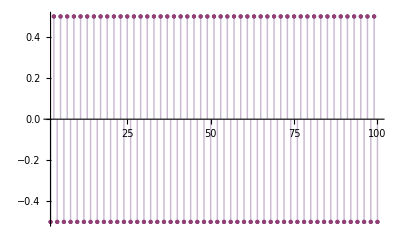

```mathematica
DiscretePlot[ {-FractionalPart[1/2 (-1+n)]+FractionalPart[n/2], ( (-1)^(n+1)/2)}, {n,2,100}]
```

```mathematica
Expand[( (-1)^(n+1)/2)-(1/2)]
```

-1/2+1/2 (-1)^(1+n)

```mathematica
SF1a[n_] :=Floor[1/2 (-1+n)]+Floor[n/2]
```

```mathematica
SF1b[n_] := n - FractionalPart[n]-1
```

```mathematica
SF1a[100]
```

99

```mathematica
Sum[ 1, {j,1,Floor[(n-1)/2]},{k,1,Floor[(Floor[n/j]-1)/2]}]
```

$Aborted

```mathematica
f1[n_] := Sum[ 1, {j,1,Floor[(n-1)/2]},{k,1,Floor[(Floor[n/j])/2]}]
```

```mathematica
f2[n_] := Sum[ 1, {j,1,Floor[(n)/2]},{k,1,Floor[(Floor[n/j]-1)/2]}]
f3[n_] := Sum[ 1, {j,1,Floor[(n-1)/2]},{k,1,Floor[(Floor[n/j]-1)/2]}]
f4[n_] := Sum[ 1, {j,1,Floor[(n)/2]},{k,1,Floor[(Floor[n/j])/2]}]
```

```mathematica
f1[100]
```

206

```mathematica
f2[100]
```

175

```mathematica
f3[100]+f4[100]-f1[100]-f2[100]
```

1

```mathematica
DE[100,2]
```

3

```mathematica
DF[100,2]
```

283

```mathematica
f3[100]+f4[100]+f1[100]+f2[100]
```

763

```mathematica
DE[n,2]
```

-∑_(j=1)^Floor[n/2] (Floor[1/2 (-1+Floor[n/(2 j)])]-Floor[1/2 Floor[n/(2 j)]])+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]-Floor[1/2 Floor[n/(1+2 j)]])

```mathematica
DF[n,1]
```

Floor[1/2 (-1+n)]+Floor[n/2]

```mathematica
FF[n_] := -∑_(j=1)^Floor[n/2] (Floor[1/2 (-1+Floor[n/(2 j)])]-Floor[1/2 Floor[n/(2 j)]])+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]-Floor[1/2 Floor[n/(1+2 j)]])
```

```mathematica
FF[100]
```

3

```mathematica
DF[n,2]
```

∑_(j=1)^Floor[n/2] (Floor[1/2 (-1+Floor[n/(2 j)])]+Floor[1/2 Floor[n/(2 j)]])+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]+Floor[1/2 Floor[n/(1+2 j)]])

```mathematica
FG[n_] := ∑_(j=1)^Floor[n/2] (Floor[1/2 (-1+Floor[n/(2 j)])]+Floor[1/2 Floor[n/(2 j)]])+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]+Floor[1/2 Floor[n/(1+2 j)]])
```

```mathematica
FG[100]
```

283

```mathematica
FF[n_] := -∑_(j=1)^Floor[n/2] (Floor[1/2 (-1+Floor[n/(2 j)])]-Floor[1/2 Floor[n/(2 j)]])+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]-Floor[1/2 Floor[n/(1+2 j)]])
FF1[n_] := -∑_(j=1)^Floor[n/2] (-1/2 + (1/2)(-1)^(1+Floor[n/(2 j)]))+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]-Floor[1/2 Floor[n/(1+2 j)]])
```

```mathematica
FF2[n_] := -∑_(j=1)^Floor[n/2] (-1/2 + (1/2)(-1)^(1+Floor[n/(2 j)]))+∑_(j=1)^Floor[1/2 (-1+n)] (-1/2+1/2 (-1)^(1+Floor[n/(1+2 j)]))
```

```mathematica
FF[1000]
```

-6

```mathematica
FF1[1000]
```

-6

```mathematica
FF2[1000]
```

-6

```mathematica
pp[n_,j_] :=Expand[Floor[1/2 (-1+Floor[n/(2 j)])]-Floor[1/2 Floor[n/(2 j)]]]
```

```mathematica
pp1[n_,j_] := -1/2 + (1/2)(-1)^(1+Floor[n/(2 j)])
```

```mathematica
Table[{n, pp[n,1], pp1[n,1]},{n,1,30}]//TableForm
```

1 | -1 | -1
2 | 0 | 0
3 | 0 | 0
4 | -1 | -1
5 | -1 | -1
6 | 0 | 0
7 | 0 | 0
8 | -1 | -1
9 | -1 | -1
10 | 0 | 0
11 | 0 | 0
12 | -1 | -1
13 | -1 | -1
14 | 0 | 0
15 | 0 | 0
16 | -1 | -1
17 | -1 | -1
18 | 0 | 0
19 | 0 | 0
20 | -1 | -1
21 | -1 | -1
22 | 0 | 0
23 | 0 | 0
24 | -1 | -1
25 | -1 | -1
26 | 0 | 0
27 | 0 | 0
28 | -1 | -1
29 | -1 | -1
30 | 0 | 0

```mathematica
Expand[ -1/2 + (1/2)(-1)^(1+Floor[n/(2 j)])]
```

-1/2+1/2 (-1)^(1+Floor[n/(2 j)])

```mathematica
px[n_,j_] :=Floor[1/2 (-1+Floor[n/(1+2 j)])]-Floor[1/2 Floor[n/(1+2 j)]]
```

```mathematica
px1[n_,j_] := -1/2 + (1/2)(-1)^(1+Floor[(n)/(2 j+1)])
```

```mathematica
Table[{n, px[n,3], px1[n,3]},{n,1,30}]//TableForm
```

1 | -1 | -1
2 | -1 | -1
3 | -1 | -1
4 | -1 | -1
5 | -1 | -1
6 | -1 | -1
7 | 0 | 0
8 | 0 | 0
9 | 0 | 0
10 | 0 | 0
11 | 0 | 0
12 | 0 | 0
13 | 0 | 0
14 | -1 | -1
15 | -1 | -1
16 | -1 | -1
17 | -1 | -1
18 | -1 | -1
19 | -1 | -1
20 | -1 | -1
21 | 0 | 0
22 | 0 | 0
23 | 0 | 0
24 | 0 | 0
25 | 0 | 0
26 | 0 | 0
27 | 0 | 0
28 | -1 | -1
29 | -1 | -1
30 | -1 | -1

```mathematica
-1/2 + (1/2)(-1)^(1+Floor[(n)/(2 j+1)])
```

-1/2+1/2 (-1)^(1+Floor[n/(1+2 j)])

```mathematica
FF2[n_] := -∑_(j=1)^Floor[n/2] (-1/2 + (1/2)(-1)^(1+Floor[n/(2 j)]))+∑_(j=1)^Floor[1/2 (-1+n)] (-1/2+1/2 (-1)^(1+Floor[n/(1+2 j)]))
```

```mathematica
FF3[n_] := ∑_(j=1)^Floor[n/2] (1/2 - (1/2)(-1)^(1+Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] (1/2-1/2 (-1)^(1+Floor[n/(1+2 j)]))
FF4[n_] := ∑_(j=1)^Floor[n/2] (1/2 + (1/2)(-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] (1/2+1/2 (-1)^Floor[n/(1+2 j)])
FF5[n_] :=(1/2)( ∑_(j=1)^Floor[n/2] (1 + (-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] (1+ (-1)^Floor[n/(1+2 j)]))
FF6[n_] :=(1/2)( ( 1/2)(1 + (-1)^n )+ ∑_(j=1)^Floor[n/2] ((-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] ((-1)^Floor[n/(1+2 j)]))
FF7[n_] :=(1/2)( ( 1/2)(1 + (-1)^n )+ ∑_(j=1)^Floor[n/2] ((-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] ((-1)^Floor[n/(1+2 j)]))
```

```mathematica
∑_(j=1)^Floor[n/2] (-1/2 + (1/2)(-1)^(1+Floor[n/(2 j)]))
```

∑_(j=1)^Floor[n/2] (-1/2+1/2 (-1)^(1+Floor[n/(2 j)]))

```mathematica
TT[n_, j_] := ((-1)^(Floor[n/(2 j)]))-((-1)^Floor[n/(1+2 j)])
```

```mathematica
TT[n,1]
```

-(-1)^Floor[n/3]+(-1)^Floor[n/2]

```mathematica
FF2[1000]
```

-6

```mathematica
FF3[1000]
```

-6

```mathematica
FF4[1000]
```

-6

```mathematica
FF5[1330]
```

-7

```mathematica
Table[ {n, FF5[n],FF6[n], FF5[n]-FF6[n] },{n,320,340}]//TableForm
```

320 | 6 | 6 | 0
321 | 8 | 8 | 0
322 | 2 | 2 | 0
323 | 4 | 4 | 0
324 | 1 | 1 | 0
325 | 5 | 5 | 0
326 | 3 | 3 | 0
327 | 5 | 5 | 0
328 | 7 | 7 | 0
329 | 9 | 9 | 0
330 | -5 | -5 | 0
331 | -5 | -5 | 0
332 | -5 | -5 | 0
333 | -1 | -1 | 0
334 | -3 | -3 | 0
335 | -1 | -1 | 0
336 | 5 | 5 | 0
337 | 5 | 5 | 0
338 | 1 | 1 | 0
339 | 3 | 3 | 0
340 | 1 | 1 | 0

```mathematica
FH1[n_] :=  ∑_(j=1)^Floor[n/2] ((-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] ((-1)^Floor[n/(1+2 j)])
```

```mathematica
FH1[1000]
```

-13

```mathematica
FH2[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,2,n}]
```

```mathematica
FH2[1000]
```

-13

```mathematica
g[n_,k_,a_]:=If[n<a^k,0,Sum[(-1)^(k-j) Binomial[k,j] g[n/a^j,k-j,a+1],{j,0,k}]];g[n_,0,a_]:=1
{$RecursionLimit=10000};
```

```mathematica
Table[ {n,g[n,2,2],E2[n,2]},{n,250,270}]//TableForm
```

250 | -2 | -2
251 | -2 | -2
252 | -6 | -6
253 | -4 | -4
254 | -6 | -6
255 | 0 | 0
256 | 7 | 7
257 | 7 | 7
258 | 1 | 1
259 | 3 | 3
260 | 1 | 1
261 | 5 | 5
262 | 3 | 3
263 | 3 | 3
264 | 5 | 5
265 | 7 | 7
266 | 1 | 1
267 | 3 | 3
268 | 3 | 3
269 | 3 | 3
270 | -11 | -11

```mathematica
E2[2,1]
```

```mathematica
LAdd[n_] := Sum[ 2^k/k,{k,1,Log[2,n]}]
```

```mathematica
LinE[n_] := LAdd[n] - Sum[ 1/k g[n,k,2],{k,1,Log[2,n]}]
```

```mathematica
LinE[100]
```

428/15

```mathematica
-g[100,5,2]
```

9

```mathematica
E2[100,5]
```

9

```mathematica
DHyp[n_,k_,a_]:=Sum[ (-1)^(k-j+m-1) Binomial[k,j] DHyp[n/(m^(k-j)),j,m+1],{m,a,n^(1/k)},{j,0,k-1}]
DHyp[n_,0,a_]:=1
```

```mathematica
DHyp[1000,3,2]
```

13

```mathematica
E2[1000,3]
```

-19

```mathematica
FF[n_] := -∑_(j=1)^Floor[n/2] (Floor[1/2 (-1+Floor[n/(2 j)])]-Floor[1/2 Floor[n/(2 j)]])+∑_(j=1)^Floor[1/2 (-1+n)] (Floor[1/2 (-1+Floor[n/(1+2 j)])]-Floor[1/2 Floor[n/(1+2 j)]])
FFI[n_] := -∑_(j=1)^(n/2) ((1/2 (-1+(n/(2 j))))-(1/2 (n/(2 j))))+∑_(j=1)^(1/2 (-1+n)) ((1/2 (-1+(n/(1+2 j))))-(1/2 (n/(1+2 j))))
```

```mathematica
FF[1000]
```

-6

```mathematica
FFI[20]
```

1/2

```mathematica
Expand[FFI[n]]
```

1/4

```mathematica
Expand[((1/2 (-1+(n/(2 j))))-(1/2 (n/(2 j))))]
```

-1/2

```mathematica
Expand[((1/2 (-1+(n/(1+2 j))))-(1/2 (n/(1+2 j))))]
```

-1/2

```mathematica
FFI[n]
```

(1-n)/4+n/4

```mathematica
FFI2[n_] := -∑_(j=1)^(n/2) ((1/2 (-1+(n/(2 j))))-(1/2 (n/(2 j))))+∑_(j=1)^(1/2 (-1+n)) ((1/2 (-1+(n/(1+2 j))))-(1/2 (n/(1+2 j))))
```

```mathematica
FFI3[n_]:=-Integrate[ ((1/2 (-1+(n/(2 j))))-(1/2 (n/(2 j)))),{j,1,n/2}]+Integrate[((1/2 (-1+(n/(1+2 j))))-(1/2 (n/(1+2 j)))),{j,1,(n-1)/2}]
```

```mathematica
FFI3[n]
```

1/4

```mathematica
-Integrate[ ((1/2 (-1+(n/(2 j))))-(1/2 (n/(2 j)))),{j,1,n/2}]
```

-1/2+n/4

```mathematica
Integrate[((1/2 (-1+(n/(1+2 j))))-(1/2 (n/(1+2 j)))),{j,1,(n-1)/2}]
```

3/4-n/4

```mathematica
FF7[n_] :=(1/2)( ( 1/2)(1 + (-1)^n )+ ∑_(j=1)^Floor[n/2] ((-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] ((-1)^Floor[n/(1+2 j)]))
```

```mathematica
FF7[100]
```

3

```mathematica
DE[100,2]
```

3

```mathematica
Table[ {n,FF7[n],DE[n,2]},{n,250,270}]//TableForm
```

250 | -2 | -2
251 | -2 | -2
252 | -6 | -6
253 | -4 | -4
254 | -6 | -6
255 | 0 | 0
256 | 7 | 7
257 | 7 | 7
258 | 1 | 1
259 | 3 | 3
260 | 1 | 1
261 | 5 | 5
262 | 3 | 3
263 | 3 | 3
264 | 5 | 5
265 | 7 | 7
266 | 1 | 1
267 | 3 | 3
268 | 3 | 3
269 | 3 | 3
270 | -11 | -11

```mathematica
TT[n_, j_] := ((-1)^(Floor[n/(2 j)]))-((-1)^Floor[n/(1+2 j)])
```

```mathematica
TT[n,1]
```

-(-1)^Floor[n/3]+(-1)^Floor[n/2]

```mathematica
TX[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,2,n}]
```

```mathematica
TY[n_] := ∑_(j=1)^Floor[n/2] ((-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] ((-1)^Floor[n/(1+2 j)])
```

```mathematica
TX[1000]
```

-13

```mathematica
TY[1000]
```

-13

```mathematica
TX[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,2,n}]
```

```mathematica
bbb = 2
TX2[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,Floor[n/(bbb+1)]+1,Floor[n/bbb]}]
Table[ {n,TX2[n],(1/2)((-1)^(bbb+1))(-(-1)^(Floor[n/bbb])-(-1)^(Floor[n/(bbb+1)]+1))},{n,50,100}]//TableForm
```

2

50 | -1 | -1
51 | 0 | 0
52 | 1 | 1
53 | 1 | 1
54 | -1 | -1
55 | -1 | -1
56 | 0 | 0
57 | 1 | 1
58 | 0 | 0
59 | 0 | 0
60 | 0 | 0
61 | 0 | 0
62 | -1 | -1
63 | 0 | 0
64 | 1 | 1
65 | 1 | 1
66 | -1 | -1
67 | -1 | -1
68 | 0 | 0
69 | 1 | 1
70 | 0 | 0
71 | 0 | 0
72 | 0 | 0
73 | 0 | 0
74 | -1 | -1
75 | 0 | 0
76 | 1 | 1
77 | 1 | 1
78 | -1 | -1
79 | -1 | -1
80 | 0 | 0
81 | 1 | 1
82 | 0 | 0
83 | 0 | 0
84 | 0 | 0
85 | 0 | 0
86 | -1 | -1
87 | 0 | 0
88 | 1 | 1
89 | 1 | 1
90 | -1 | -1
91 | -1 | -1
92 | 0 | 0
93 | 1 | 1
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 0 | 0
98 | -1 | -1
99 | 0 | 0
100 | 1 | 1

```mathematica
(1/2)((-1)^(ccc))((-1)^(Floor[n/ccc])-(-1)^(Floor[n/(ccc+1)]))
```

1/2 (-1)^ccc ((-1)^Floor[n/ccc]-(-1)^Floor[n/(1+ccc)])

```mathematica
u = 5
TX2[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,Floor[n/(u+1)]+1,Floor[n/u]}]
Table[ {n,TX2[n],(1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))},{n,50,100}]//TableForm
```

5

50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 0 | 0
54 | -1 | -1
55 | 0 | 0
56 | 0 | 0
57 | 0 | 0
58 | 0 | 0
59 | 0 | 0
60 | 0 | 0
61 | 0 | 0
62 | 0 | 0
63 | 0 | 0
64 | 0 | 0
65 | 1 | 1
66 | 0 | 0
67 | 0 | 0
68 | 0 | 0
69 | 0 | 0
70 | -1 | -1
71 | -1 | -1
72 | 0 | 0
73 | 0 | 0
74 | 0 | 0
75 | 1 | 1
76 | 1 | 1
77 | 1 | 1
78 | 0 | 0
79 | 0 | 0
80 | -1 | -1
81 | -1 | -1
82 | -1 | -1
83 | -1 | -1
84 | 0 | 0
85 | 1 | 1
86 | 1 | 1
87 | 1 | 1
88 | 1 | 1
89 | 1 | 1
90 | -1 | -1
91 | -1 | -1
92 | -1 | -1
93 | -1 | -1
94 | -1 | -1
95 | 0 | 0
96 | 1 | 1
97 | 1 | 1
98 | 1 | 1
99 | 1 | 1
100 | 0 | 0

```mathematica
u = 2
TX2[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,Floor[n/(u+2)]+1,Floor[n/u]}]
Table[ {n,TX2[n],(1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))+(1/2)((-1)^(u+1))((-1)^(Floor[n/(u+1)])-(-1)^(Floor[n/(u+2)]))},{n,50,100}]//TableForm
```

2

50 | -1 | -1
51 | 1 | 1
52 | 1 | 1
53 | 1 | 1
54 | -2 | -2
55 | -2 | -2
56 | 0 | 0
57 | 2 | 2
58 | 1 | 1
59 | 1 | 1
60 | -1 | -1
61 | -1 | -1
62 | -2 | -2
63 | 0 | 0
64 | 2 | 2
65 | 2 | 2
66 | -1 | -1
67 | -1 | -1
68 | -1 | -1
69 | 1 | 1
70 | 0 | 0
71 | 0 | 0
72 | 0 | 0
73 | 0 | 0
74 | -1 | -1
75 | 1 | 1
76 | 1 | 1
77 | 1 | 1
78 | -2 | -2
79 | -2 | -2
80 | 0 | 0
81 | 2 | 2
82 | 1 | 1
83 | 1 | 1
84 | -1 | -1
85 | -1 | -1
86 | -2 | -2
87 | 0 | 0
88 | 2 | 2
89 | 2 | 2
90 | -1 | -1
91 | -1 | -1
92 | -1 | -1
93 | 1 | 1
94 | 0 | 0
95 | 0 | 0
96 | 0 | 0
97 | 0 | 0
98 | -1 | -1
99 | 1 | 1
100 | 1 | 1

```mathematica
u = 2
Expand[(1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))+(1/2)((-1)^(u+1))((-1)^(Floor[n/(u+1)])-(-1)^(Floor[n/(u+2)]))]
```

2

1/2 (-1)^Floor[n/4]-(-1)^Floor[n/3]+1/2 (-1)^Floor[n/2]

```mathematica
u = 2
TX2[n_] := Sum[ (-1)^(j+Floor[n/j]),{j,Floor[n/(u+3)]+1,Floor[n/u]}]
Table[ {n,TX2[n],(1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))
+(1/2)((-1)^(u+1))((-1)^(Floor[n/(u+1)])-(-1)^(Floor[n/(u+2)]))
+(1/2)((-1)^(u+2))((-1)^(Floor[n/(u+2)])-(-1)^(Floor[n/(u+3)]))},{n,50,100}]//TableForm
```

2

50 | -1 | -1
51 | 1 | 1
52 | 0 | 0
53 | 0 | 0
54 | -3 | -3
55 | -2 | -2
56 | 1 | 1
57 | 3 | 3
58 | 2 | 2
59 | 2 | 2
60 | -2 | -2
61 | -2 | -2
62 | -3 | -3
63 | -1 | -1
64 | 2 | 2
65 | 3 | 3
66 | 0 | 0
67 | 0 | 0
68 | -1 | -1
69 | 1 | 1
70 | -1 | -1
71 | -1 | -1
72 | 0 | 0
73 | 0 | 0
74 | -1 | -1
75 | 2 | 2
76 | 1 | 1
77 | 1 | 1
78 | -2 | -2
79 | -2 | -2
80 | 0 | 0
81 | 2 | 2
82 | 1 | 1
83 | 1 | 1
84 | -2 | -2
85 | -1 | -1
86 | -2 | -2
87 | 0 | 0
88 | 3 | 3
89 | 3 | 3
90 | -1 | -1
91 | -1 | -1
92 | -2 | -2
93 | 0 | 0
94 | -1 | -1
95 | 0 | 0
96 | 1 | 1
97 | 1 | 1
98 | 0 | 0
99 | 2 | 2
100 | 0 | 0

```mathematica
(1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))
+(1/2)((-1)^(u+1))((-1)^(Floor[n/(u+1)])-(-1)^(Floor[n/(u+2)]))
+(1/2)((-1)^(u+2))((-1)^(Floor[n/(u+2)])-(-1)^(Floor[n/(u+3)]))
```

1/2 (-(-1)^Floor[n/5]+(-1)^Floor[n/4])+1/2 ((-1)^Floor[n/4]-(-1)^Floor[n/3])+1/2 (-(-1)^Floor[n/3]+(-1)^Floor[n/2])

```mathematica
u = 2
Expand[ (1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))
+(1/2)((-1)^(u+1))((-1)^(Floor[n/(u+1)])-(-1)^(Floor[n/(u+2)]))
+(1/2)((-1)^(u+2))((-1)^(Floor[n/(u+2)])-(-1)^(Floor[n/(u+3)]))]
```

2

-1/2 (-1)^Floor[n/5]+(-1)^Floor[n/4]-(-1)^Floor[n/3]+1/2 (-1)^Floor[n/2]

```mathematica
e2[100,5]
```

0

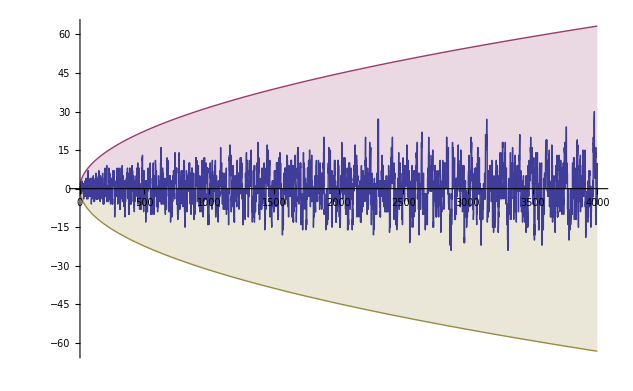

```mathematica
DiscretePlot[ {E2[n,2],n^(1/2),-(n^(1/2))},{n,2,4000}]
```

```mathematica
1000^(.25)
```

5.62341

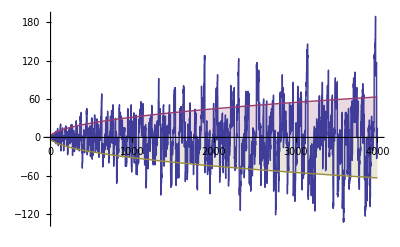

```mathematica
DiscretePlot[ {E2[n,3],n^(1/2),-(n^(1/2))},{n,2,4000}]
```

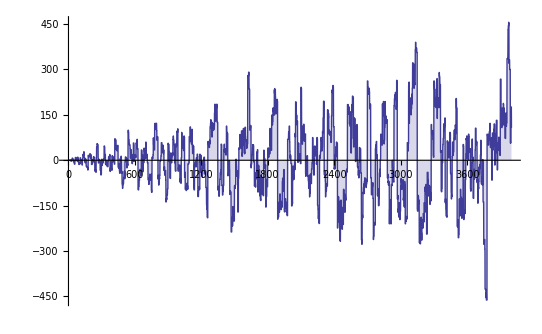

```mathematica
DiscretePlot[ {E2[n,4]},{n,2,4000}]
```

```mathematica
D2Alt[n_,k_]:=D2Alt[n,k]=Sum[D2Alt[Floor[n/j],k-1],{j,2,n}];D2Alt[n_,0]:=1
```

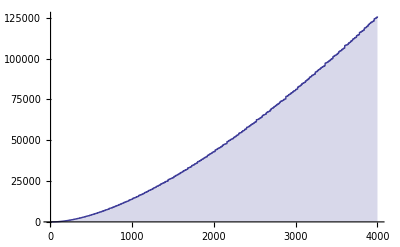

```mathematica
DiscretePlot[ {D2Alt[n,4]},{n,2,4000}]
```

```mathematica
PrimePi[4000]
```

550

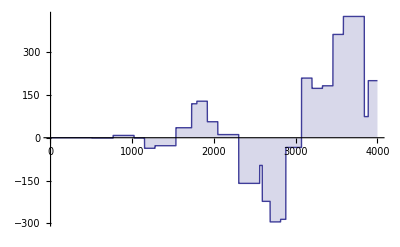

```mathematica
DiscretePlot[ {E2[n,9]},{n,2,4000}]
```

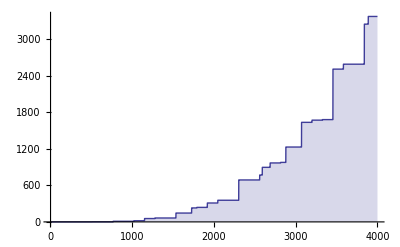

```mathematica
DiscretePlot[ {D2Alt[n,9]},{n,2,4000}]
```

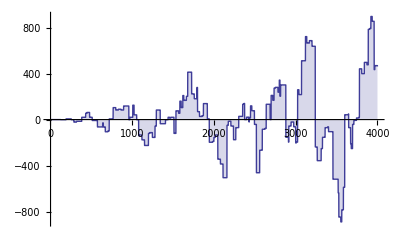

```mathematica
DiscretePlot[ {E2[n,7]},{n,2,4000}]
```

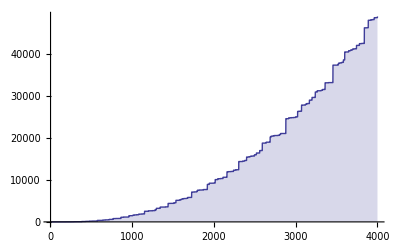

```mathematica
DiscretePlot[ {D2Alt[n,7]},{n,2,4000}]
```

```mathematica
LAdd[n_] := Sum[ 2^k/k,{k,1,Log[2,n]}]
```

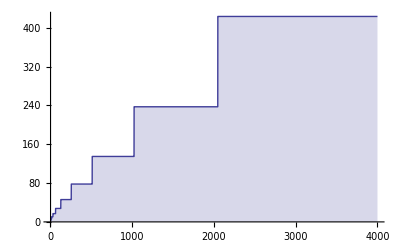

```mathematica
DiscretePlot[ {LAdd[n]},{n,2,4000}]
```

```mathematica
LAdd[100]+L2[100]
```

428/15

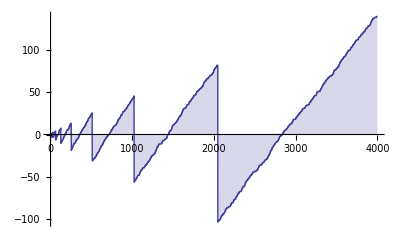

```mathematica
DiscretePlot[ {L2[n]},{n,2,4000}]
```

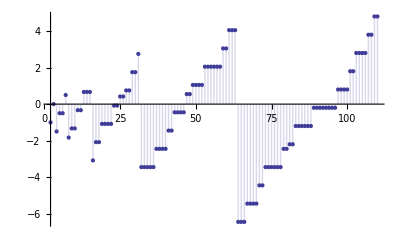

```mathematica
DiscretePlot[ {L2[n]},{n,2,110}]
```

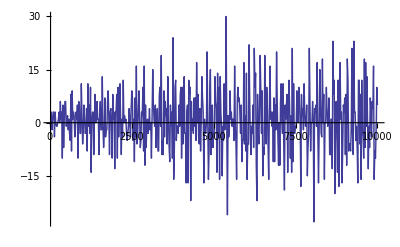

```mathematica
DiscretePlot[ {E2[n,2]},{n,20,10000,20}]
```

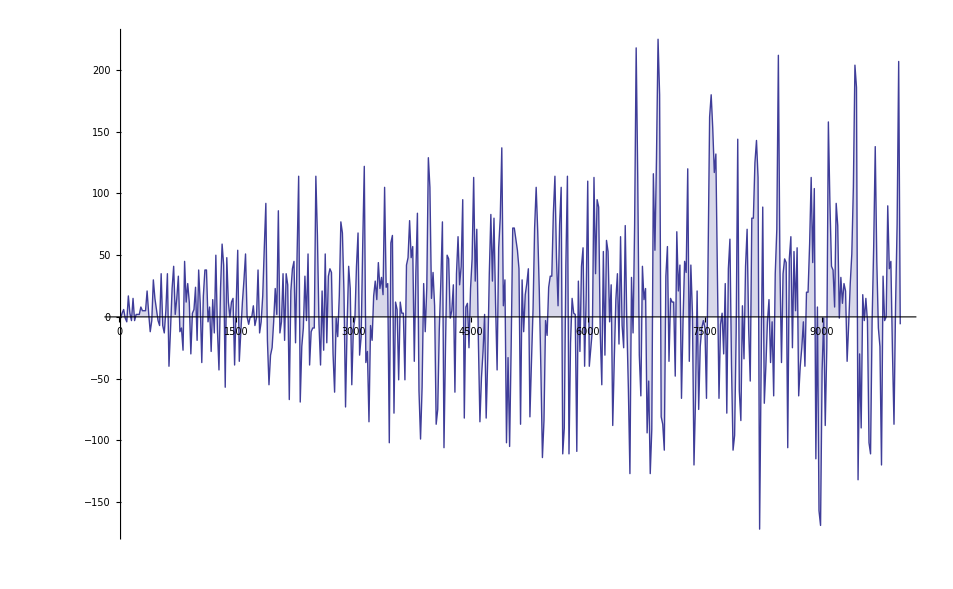
-Graphics-/3

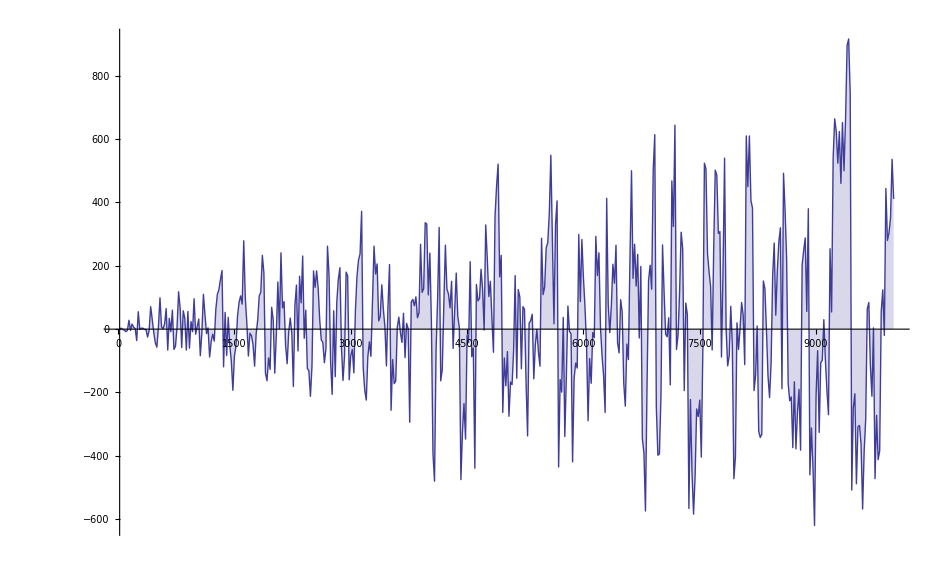
--Graphics-/4

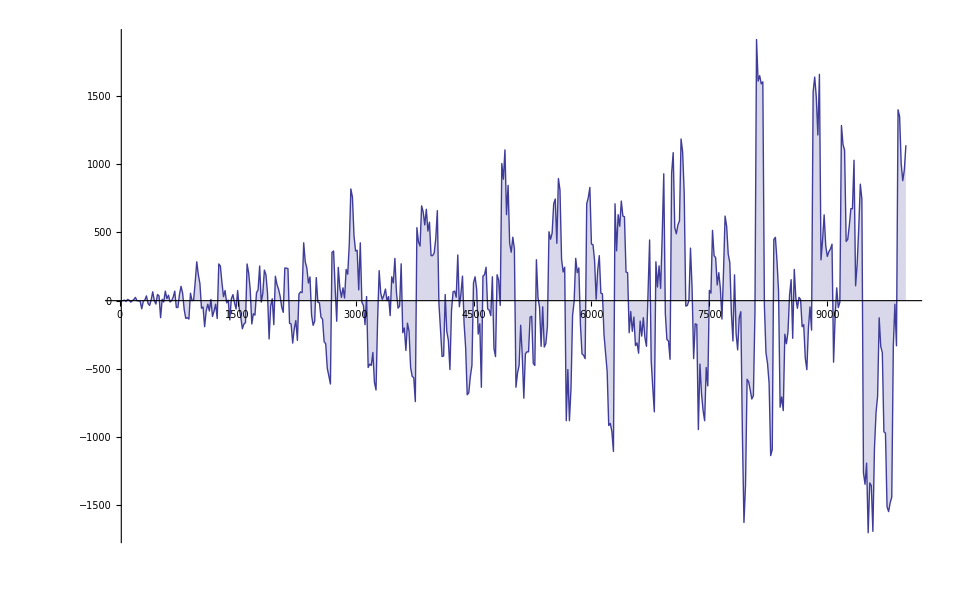
-Graphics-/5

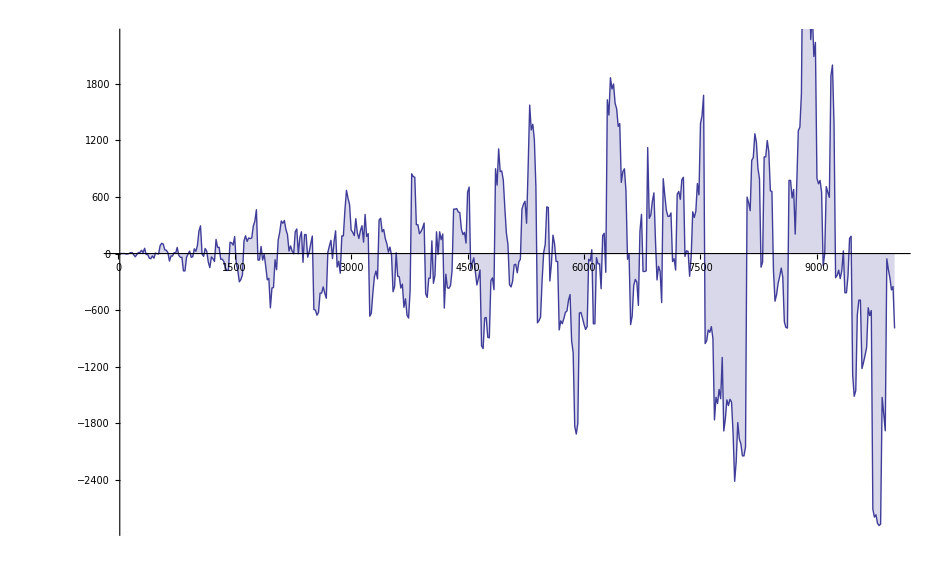
--Graphics-/6

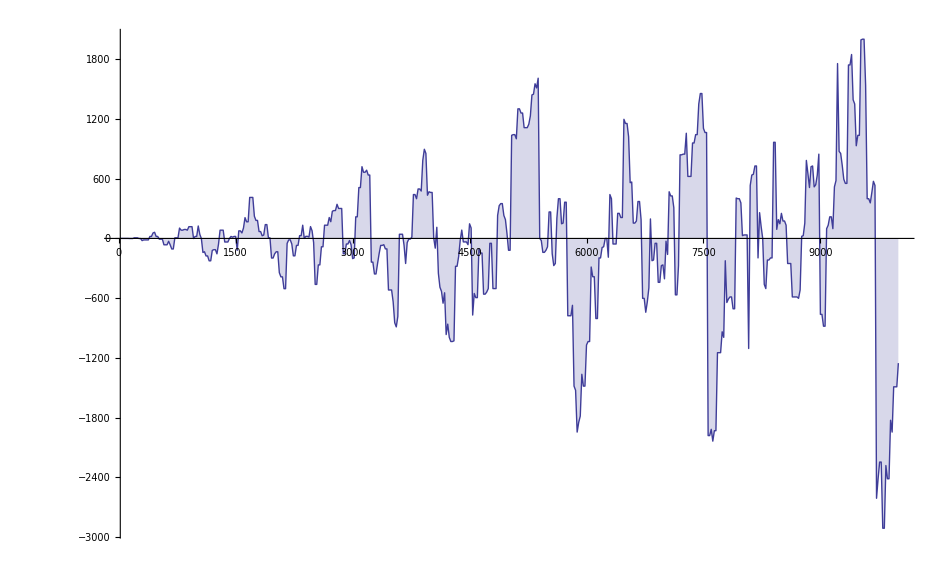
-Graphics-/7

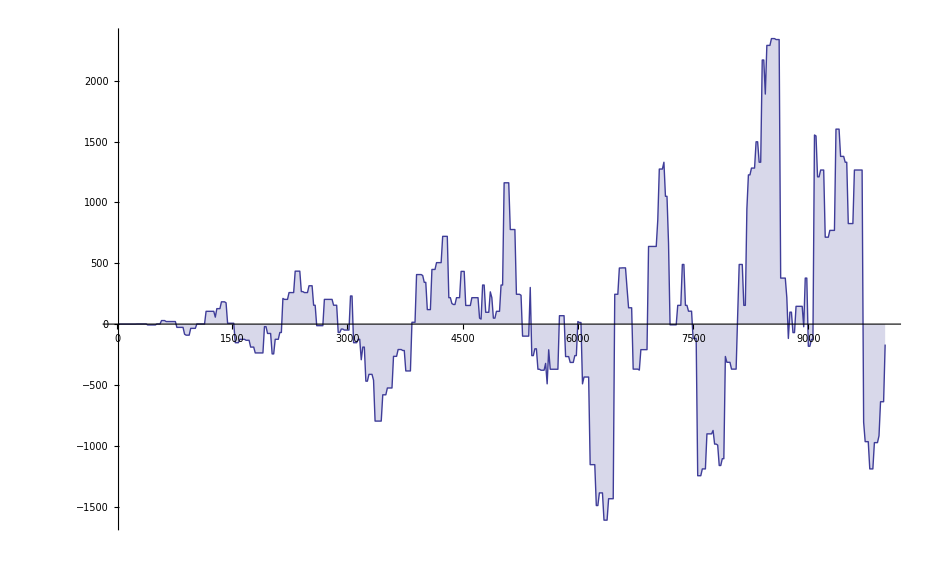
--Graphics-/8

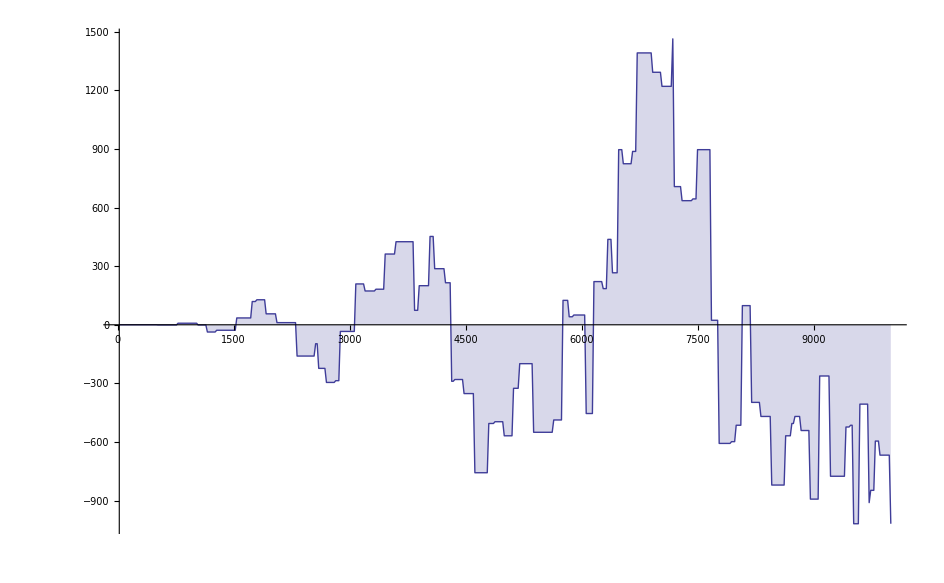
-Graphics-/9

```mathematica
DiscretePlot[ {E2[n,3]},{n,20,10000,20}]/3
DiscretePlot[ {E2[n,4]},{n,20,10000,20}]/-4
DiscretePlot[ {E2[n,5]},{n,20,10000,20}]/5
DiscretePlot[ {E2[n,6]},{n,20,10000,20}]/-6
DiscretePlot[ {E2[n,7]},{n,20,10000,20}]/7
DiscretePlot[ {E2[n,8]},{n,20,10000,20}]/-8
DiscretePlot[ {E2[n,9]},{n,20,10000,20}]/9
```

```mathematica
Table[{n,l2[2^n], pk[2^n]},{n,1,8}]//TableForm
```

1 | -1 | -1
2 | -3/2 | -3/2
3 | -7/3 | -7/3
4 | -15/4 | -15/4
5 | -31/5 | -31/5
6 | -21/2 | -21/2
7 | -127/7 | -127/7
8 | -255/8 | -255/8

```mathematica
E2[100,2]
```

3

```mathematica
FF7[n_] :=(1/2)( ( 1/2)(1 + (-1)^n )+ ∑_(j=1)^Floor[n/2] ((-1)^(Floor[n/(2 j)]))-∑_(j=1)^Floor[1/2 (-1+n)] ((-1)^Floor[n/(1+2 j)]))
```

```mathematica
FF8[n_] :=(1/2)( ( 1/2)(1 + (-1)^n )+ Sum[ (-1)^(j+Floor[n/j]),{j,2,n}])
```

```mathematica
FF9[n_] :=(1/2)( ( 1/2)(1 + (-1)^n )+ Sum[ (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]+ Sum[ (-1)^(j+Floor[n/j]),{j,1,Floor[n/Floor[n^(1/2)]-1]}] )
```

```mathematica
Table[ {n, FF7[n],FF9[n]},{n,80,100}]//TableForm
```

80 | 1 | 1/2
81 | 4 | 4
82 | 2 | 3/2
83 | 2 | 2
84 | 0 | -1/2
85 | 2 | 2
86 | 0 | -1/2
87 | 2 | 2
88 | 4 | 7/2
89 | 4 | 4
90 | -6 | -6
91 | -4 | -7/2
92 | -4 | -4
93 | -2 | -3/2
94 | -4 | -4
95 | -2 | -3/2
96 | 4 | 4
97 | 4 | 9/2
98 | 0 | 0
99 | 4 | 4
100 | 3 | 5/2

```mathematica
FF8[100]
```

3

```mathematica
-6
```

```mathematica
FF9[100]
```

5/2

```mathematica
u = 2
Expand[ (1/2)((-1)^(u))((-1)^(Floor[n/u])-(-1)^(Floor[n/(u+1)]))
+(1/2)((-1)^(u+1))((-1)^(Floor[n/(u+1)])-(-1)^(Floor[n/(u+2)]))
+(1/2)((-1)^(u+2))((-1)^(Floor[n/(u+2)])-(-1)^(Floor[n/(u+3)]))]
```

2

-1/2 (-1)^Floor[n/5]+(-1)^Floor[n/4]-(-1)^Floor[n/3]+1/2 (-1)^Floor[n/2]

```mathematica
fe1[n_]:=Sum[ (-1)^(j+Floor[n/j]),{j,1,Floor[n/Floor[n^(1/2)]-1]}]
```

```mathematica
fe1[1000]
```

-7

```mathematica
ee1[n_] :=Sum[ (-1)^j (-1)^k,{j,2,n},{k,2,Floor[n/j]}]
```

```mathematica
ee1[100]
```

3

```mathematica
ee1[1000]
```

-6

```mathematica
ee1a[n_] :=2 Sum[ (-1)^j (-1)^k,{j,2,Floor[n^(1/2)]},{k,2,Floor[n/j]}]-Sum[ (-1)^j (-1)^k,{j,2,Floor[n^(1/2)]},{k,2,Floor[n^(1/2)]}]
```

```mathematica
ee1a[1000]
```

-6

```mathematica
ee1b[n_] :=2 Sum[ (-1)^j (-1)^k,{j,2,Floor[n^(1/2)]},{k,2,Floor[n/j]}]-1/2 (1+(-1)^Floor[√n])

ee1b[1000]
```

-6

```mathematica
ee1a1[n_] :=Sum[ (-1)^j (-1)^k,{j,2,Floor[n^(1/2)]},{k,2,Floor[n^(1/2)]}]
```

```mathematica
Table[ {n, ee1a1[n], 1/2 + (1/2)(-1)^(Floor[n^(1/2)])},{n,2,50}]//TableForm
```

2 | 0 | 0
3 | 0 | 0
4 | 1 | 1
5 | 1 | 1
6 | 1 | 1
7 | 1 | 1
8 | 1 | 1
9 | 0 | 0
10 | 0 | 0
11 | 0 | 0
12 | 0 | 0
13 | 0 | 0
14 | 0 | 0
15 | 0 | 0
16 | 1 | 1
17 | 1 | 1
18 | 1 | 1
19 | 1 | 1
20 | 1 | 1
21 | 1 | 1
22 | 1 | 1
23 | 1 | 1
24 | 1 | 1
25 | 0 | 0
26 | 0 | 0
27 | 0 | 0
28 | 0 | 0
29 | 0 | 0
30 | 0 | 0
31 | 0 | 0
32 | 0 | 0
33 | 0 | 0
34 | 0 | 0
35 | 0 | 0
36 | 1 | 1
37 | 1 | 1
38 | 1 | 1
39 | 1 | 1
40 | 1 | 1
41 | 1 | 1
42 | 1 | 1
43 | 1 | 1
44 | 1 | 1
45 | 1 | 1
46 | 1 | 1
47 | 1 | 1
48 | 1 | 1
49 | 0 | 0
50 | 0 | 0

```mathematica
FullSimplify[Expand[(1/2 + (1/2)(-1)^(Floor[n^(1/2)]))]]
```

1/2 (1+(-1)^Floor[√n])

```mathematica
Sum[ (-1)^j (-1)^k,{j,2,Floor[n^(1/2)]},{k,2,Floor[n/j]}]
```

$Aborted

```mathematica
Sum[ (-1)^j ,{j,2,n}]
```

1/2 (1+(-1)^n)

```mathematica
ee1b[n_] :=2 Sum[ (-1)^j (-1)^k,{j,2,Floor[n^(1/2)]},{k,2,Floor[n/j]}]-1/2 (1+(-1)^Floor[√n])
```

```mathematica
ee1c[n_] :=2 Sum[ (-1)^j (1/2 (1+(-1)^Floor[n/j])),{j,2,Floor[n^(1/2)]}]-1/2 (1+(-1)^Floor[√n])
```

```mathematica
ee1c[100]
```

3

```mathematica
ee1d[n_] :=2 Sum[ (-1)^j/2+1/2 (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]-1/2 (1+(-1)^Floor[√n])
```

```mathematica
ee1e[n_] :=2 Sum[ (-1)^j/2,{j,2,Floor[n^(1/2)]}]+2 Sum[ 1/2 (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]-1/2 (1+(-1)^Floor[√n])
```

```mathematica
ee1e[1000]
```

-6

```mathematica
ee1f[n_] := Sum[ (-1)^j,{j,2,Floor[n^(1/2)]}]+ Sum[  (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]-1/2 (1+(-1)^Floor[√n])
```

```mathematica
ee1f[1000]
```

-6

```mathematica
ee1g[n_] := 1/2 (1+(-1)^Floor[√n])+ Sum[  (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]-1/2 (1+(-1)^Floor[√n])
```

```mathematica
ee1g[1000]
```

-6

```mathematica
ee1h[n_] :=Sum[  (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]
```

```mathematica
ee1h[1000]
```

-6

```mathematica
Sum[  (-1)^(j+Floor[n/j]),{j,2,Floor[n^(1/2)]}]
```

∑_(j=2)^Floor[√n] (-1)^(j+Floor[n/j])

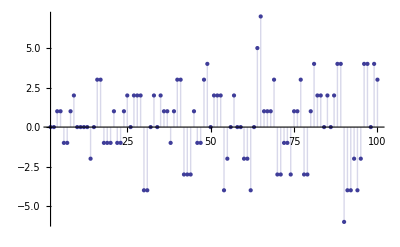

```mathematica
DiscretePlot[ ee1h[n],{n,2,100}]
```

```mathematica
Sum[ (-1)^j ,{j,m,n}]
```

1/2 ((-1)^m+(-1)^n)